```mathematica
data =Import["C:\\Users\\Juhász Nóra\\Documents\\GitHub\\ABM-PDE\\StochasticVariability\\theo_results\\theo18.txt", "Table"];
```

dataLength will be 1000, this was just an experiment

```mathematica
dataLength=1000;
```

```mathematica
cleanData={};
```

```mathematica
For[i=1,i<=dataLength, i++,cleanData=Append[cleanData,data[[i]][[4]]]]
```

```mathematica
cleanData;
```

```mathematica
probabilityData={};
```

```mathematica
For[i=0,i<=Max[cleanData], i++,probabilityData=Append[probabilityData,{i,0}]]
```

```mathematica
probabilityData;
```

```mathematica
For[i=1,i<=dataLength, i++,probabilityData[[cleanData[[i]]+1,2]]=probabilityData[[cleanData[[i]]+1,2]] + 1]
```

```mathematica
probabilityData
```

{{0,466},{1,249},{2,148},{3,64},{4,38},{5,18},{6,7},{7,4},{8,5},{9,1}}

```mathematica
N[Sum[probabilityData[[i,1]]*probabilityData[[i,2]]/1000,{i,1,Length[probabilityData]}]]
```

1.098

```mathematica
probDensFunc[x_]:=N[probabilityData[[x+1,2]]/dataLength]
```

```mathematica
probDensFunc[0]
```

0.466

http://math.bme.hu/~nandori/Virtual_lab/stat/expect/Generating.pdf

```mathematica
probGenFunc[z_]:=Sum[probDensFunc[n]*(z^n),{n,0,Max[cleanData]}]
```

```mathematica
probGenFunc[0.01]
```

0.468505

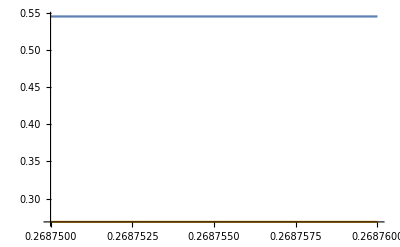

```mathematica
Plot[{probGenFunc[t],t},{t,0.26875,0.26876}]
```

```mathematica
probGenFunc[0.2687]
```

0.54506